## Init

```mathematica
(*EINZIG PATH*)
```

```mathematica
rawPass=StringSplit[#," # "]&/@StringSplit[raw,{"\n"}];
```

```mathematica
Length@rawPass==6428632
```

True

```mathematica
id=rawPass[[;;,1]];
```

```mathematica
usrName=rawPass[[;;,3]];
```

```mathematica
psk=rawPass[[;;,2]];
```

## Functions

```mathematica
elementAnalysis[pskList_]:=Module[{charGroups},charGroups=Flatten@StringCases[pskList,{DigitCharacter->"Numbers",LetterCharacter->"Letters",Except[DigitCharacter|LetterCharacter]->"Others"}];
Counts[charGroups]]
elementAnalysisShort[pskList_]:=Module[{charGroups},charGroups=Flatten@StringReplace[pskList,{DigitCharacter->"n",LetterCharacter->"l",Except[DigitCharacter|LetterCharacter]->"o"}];
Counts[charGroups]]
```

```mathematica
pyTab=Flatten@DeleteDuplicates@StringSplit["ba bo bi bu bai bei bao bie ban ben bin bang beng bing biao bian pa po pi pu pai pei pao pou pie pan pen pin pang peng ping piao pian ma mo me mi mu mai mei mao mou miu mie man men min mang meng ming miao mian fa fo fu fei fou fan fen fang feng da de di du dai dei dui dao dou diu die dan den dun dang deng ding dong dia diao dian duo duan ta te tu tai tui tao tou tie tan tun tang teng ting tong tiao tian tuo tuan na ne ni nu nai nei nao nou niu nie nan nen nin nun nang neng ning nong niao nian niang nuo nuan la le li lu lv lai lei lao lou liu lie lve lan lin lun lang leng ling long lia liao lian liang luo luan ge gu gai gei gui gao gou gan gen gun gang geng gong gua guo guai guan guang ka ke ku kai kei kui kao kou kan ken kun kang keng kong kua kuo kuai kuan kuang ha he hu hai hei hui hao hou han hen hun hang heng hong hua huo huai huan huang ju jiu jie jue jin jun jing jia jiao jian jiang jiong juan qi qu qiu qie que qin qun qing qia qiao qian qiang qiong quan xi xu xiu xie xue xin xun xing xia xiao xian xiang xiong xuan zha zhe zhi zhu zhai zhui zhao zhou zhan zhen zhun zhang zheng zhong zhua zhuo zhuai zhuan zhuang cha che chi chu chai chui chao chou chan chen chun chang cheng chong chua chuo chuai chuan chuang sha she shi shu shai shei shui shao shou shan shen shun shang sheng shua shuo shuai shuan shuang re ri ru rui rao rou ran ren run rang reng rong ruo ruan za ze zi zu zai zei zui zao zou zan zen zun zang zeng zong zuo zuan ca ce ci cu cai cui cao cou can cen cun cang ceng cong cuo cuan sa se si su sai sui sao sou san sen sun sang seng song suo ya ye yi yu yao you yue yan yin yun yang ying yong yuan yuan wo wu wai wei wan wen wang weng",{" ","\n"}];
```

```mathematica
datePatternAnalysis[pskList_]:=Module[{dateFormats},
patterns={"Year","Month","Day"};

]
```

```mathematica
englishWordAnalysis[pskList_]:=Module[{words},words=Select[pskList,DictionaryLookup[#]!={}&];
Tally[words]]
```

```mathematica
keyboardRows={"1234567890-=","qwertyuiop[]","asdfghjkl;'","zxcvbnm,./"};
```

```mathematica
keyboardAdjacency=StringCases[keyboardRows,x__/;StringLength[x]>=6,Overlaps->All];
```

```mathematica
keyboardAdjacencyAnalysis[psk_List]:=Select[psk,StringContainsQ[keyboardAdjacency]]
```

## Calling

### Element Analysis

```mathematica
eA=elementAnalysis[psk];
```

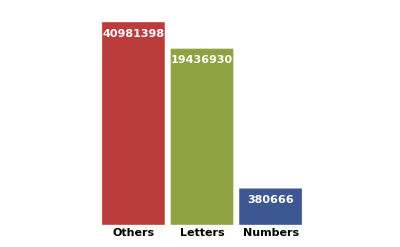

```mathematica
BarChart[eA,
ColorFunction->ColorData["DarkRainbow"],
ScalingFunctions->"Log",
ChartLabels->Placed[(Style[#,Black,Larger,Bold]&/@{"Others","Letters","Numbers"}),Below],
Axes->False,
LabelingFunction->Top,
LabelStyle->Directive[Bold,White,Larger],
Background->White
]
```

```mathematica
charactersElements=Reverse[Sort[elementAnalysisShort[psk]]];
```

```mathematica
Flatten@StringCases[psk,___~~""~~___]
```

{casterisme,casterlucifer,skycaster,caster47,lancaster,22casters}

```mathematica
Flatten[StringCases[psk,Repeated[LetterCharacter,{8}]]][[;;30]]
```

{hebeibdh,priverhe,toadswan,blackswo,mirandal,jamstang,robinson,cxlightt,earthwor,clonepig,Mylovedn,tungsten,hudahycs,westwood,pdcsetpd,zhongsha,xiapeter,mcmaster,password,onnihili,liuhualo,sourcess,leozhong,ifuckyou,sineysof,netinfan,lovebobo,dzmaadzm,dvlpment,alskdjfh}

```mathematica
charactersElementsList=KeyValueMap[#1->#2&,charactersElements];
```

```mathematica
charactersElementsReTop=Thread[StringReplace[charactersElementsList[[;;20,1]],b:(Shortest[n_]..):>ToUpperCase[n]<>ToString[StringLength[b]]]->charactersElementsList[[;;20,2]]];
```

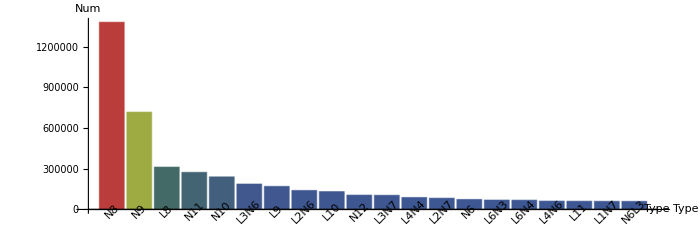

```mathematica
BarChart[charactersElementsReTop[[;;,2]],ChartLabels->Placed[charactersElementsReTop[[;;,1]],Axis,Rotate[#,Pi/4]&],
ColorFunction->ColorData["DarkRainbow"],
AspectRatio->1/3,
ImageSize->700,
LabelStyle->Directive[Black,Bold,15,FontFamily->"Times"],
AxesStyle->Directive[Black,Bold, 16],
AxesLabel->{"\nType","Num"}
]
```

```mathematica
lenSortPsk=SortBy[psk,StringLength];
```

```mathematica
lenSortPskList=Gather[lenSortPsk,StringLength[#1]==StringLength[#2]&];
```

```mathematica
combinationsEz=Flatten[StringCases[#,
{StartOfString~~x:DigitCharacter..~~EndOfString:>"onlyNumbers",
StartOfString~~n:DigitCharacter..~~x:LetterCharacter..~~EndOfString:>("num+letter"),
StartOfString~~x:LetterCharacter..~~EndOfString:>"onlyLetters",
StartOfString~~n:LetterCharacter..~~x:DigitCharacter..~~EndOfString:>("letter+num"),
StartOfString~~DigitCharacter..~~Except[DigitCharacter|LetterCharacter]..~~EndOfString:>"num+others",
StartOfString~~LetterCharacter..~~Except[DigitCharacter|LetterCharacter]..~~EndOfString:>"letter+others",
StartOfString~~""~~EndOfString:>"noPsk"}]/.{}->{"NotMatched"}]&/@lenSortPskList;
```

```mathematica
combinations=StringCases[lenSortPsk,
{StartOfString~~x:DigitCharacter..~~EndOfString:>"onlyNumbers@"<>ToString@StringLength[x],
StartOfString~~n:DigitCharacter..~~x:LetterCharacter..~~EndOfString:>("num@"<>ToString@StringLength[n]<>"+letter@"<>ToString@StringLength[x]),
StartOfString~~x:LetterCharacter..~~EndOfString:>"onlyLetters@"<>ToString@StringLength[x],
StartOfString~~n:LetterCharacter..~~x:DigitCharacter..~~EndOfString:>("letter@"<>ToString@StringLength[n]<>"+num@"<>ToString@StringLength[x]),
StartOfString~~DigitCharacter..~~Except[DigitCharacter|LetterCharacter]..~~EndOfString:>"num+others",
StartOfString~~LetterCharacter..~~Except[DigitCharacter|LetterCharacter]..~~EndOfString:>"letter+others",
StartOfString~~""~~EndOfString:>"noPsk"}]/.{}->{"NotMatched"};
```

```mathematica
combinationsEzData=KeyValueMap[#1->#2&,Reverse[Sort[Counts[#]]]]&/@combinationsEz;
```

```mathematica
toCallOut[x_]:=Map[Callout[#[[2]],#[[1]]]&,x,{2}]
```

```mathematica
sel=Select[combinationsEzData,Total[#[[;;,2]]]>350000&];
head=DeleteDuplicates[Flatten@sel[[;;,;;,1]]];
```

```mathematica
drColor=Reverse[ColorData["DarkRainbow"]/@Array[#&,7,{0,1}]];
colorLabel[x_]:=drColor[[First@@Position[head,x]]];
```

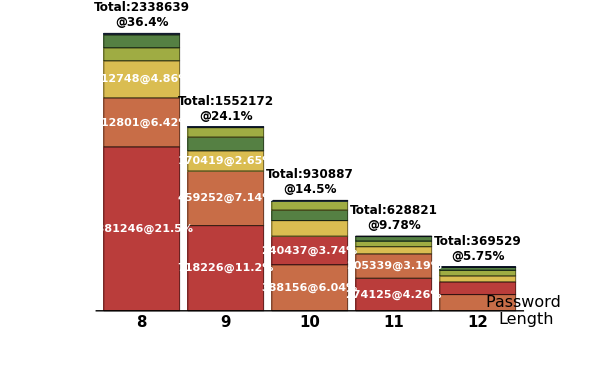

```mathematica
Legended[BarChart[Map[
Labeled[
Style[#[[2]],colorLabel[#[[1]]]],
Style[
If[#[[2]]>170000,ToString[#[[2]]]<>"@"<>ToString[NumberForm[#[[2]]/Length[psk] 100.,3]]<>"%",""],Bold,White,Larger

],Center]&,
sel,{2}],
ChartLayout->"Stacked",
(*ImagePadding->{{100,100},{0,0}},*)
ImageSize->600,
Axes->{True,False},
AxesLabel->{Style["Password \nLength",Black,16,FontFamily->"Times"],Style["Number",Bold,FontFamily->"Arial"]},
ChartLabels->{Placed[{Style[ToString[#],Bold,15]&/@Range[8,14],Style["Total:"<>ToString[#]<>"\n@"<>ToString[NumberForm[#/Length[psk] 100.,3]]<>"%",Bold,12]&/@Total[sel[[;;,;;,2]]ᵀ]},{Below,Above}],Placed[{""},Top]},
AxesStyle->Directive[Black,Larger],

Background->White

]
,Column[Table[Row[{drColor[[i]],Style[head[[i]],Black,16,FontFamily->"Times"]}],{i,Length@head}]]
]
```

### Character Analysis

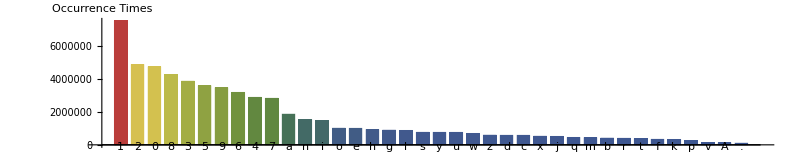

```mathematica
BarChart[Select[CharacterCounts[StringJoin[psk]],#>100000&],
ChartLabels->Automatic,
AspectRatio->1/5,
Background->White,
ColorFunction->ColorData["DarkRainbow"],
LabelStyle->Directive[Black,Bold,15,FontFamily->"Times"],
AxesStyle->Directive[Black,Bold, 16],
AxesLabel->"Occurrence\nTimes"

]
```

```mathematica
azLower=Lookup[CharacterCounts[StringJoin[psk]],CharacterRange["a","z"]];
azUpper=Lookup[CharacterCounts[StringJoin[psk]],CharacterRange["A","Z"]];
```

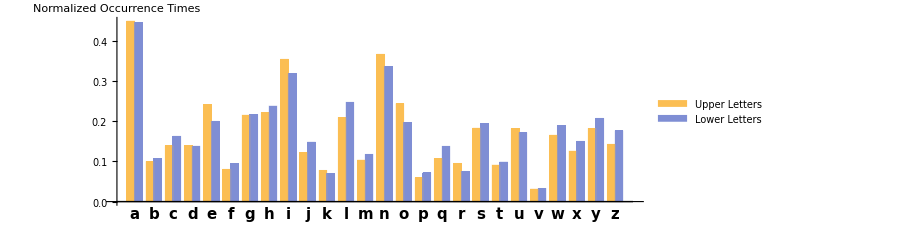

```mathematica
BarChart[{Normalize@azLower,Normalize@azUpper}ᵀ,
BarSpacing->{0,.5},
AspectRatio->1/3,
ImageSize->800,
ChartLabels->{Placed[CharacterRange["a","z"],Below],None},
ChartLegends->{"Upper Letters","Lower Letters"},
LabelStyle->Directive[Black,Bold,15,FontFamily->"Times"],
AxesStyle->Directive[Black,Bold, 16],
AxesLabel->"Normalized\nOccurrence Times"

]
```

### Length Analysis

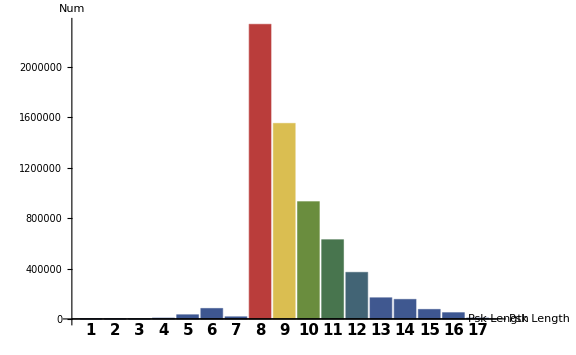

```mathematica
BarChart[SortBy[KeyValueMap[#1->#2&,Counts[StringLength/@psk]],#1&][[;;17,2]],ColorFunction->ColorData["DarkRainbow"],ChartLabels->Placed[Range[1,17],Below],ImageSize->Large,LabelStyle->Directive[Black,Bold,15,FontFamily->"Times"],AxesStyle->Directive[Black,Bold,16],AxesLabel->{"\nPsk Length","Num"}]
```

### Date Analysis

```mathematica
digit6=Flatten@StringCases[psk,Repeated[DigitCharacter,{6}]];
digit8=Flatten@StringCases[psk,Repeated[DigitCharacter,{8}]];
Off[FromDateString::str]
Off[FromDateString::ambig]
Date1Q[str_]:=StringMatchQ[str,DatePattern[{"Month","Day","Year"}]|DatePattern[{"Day","Month","Year"}]|DatePattern[{"Year","Month","Day"}]]
```

```mathematica
dateStringSeparate6[str_]:=StringCases[str,StartOfString~~a1:Repeated[DigitCharacter,{2}]~~a2:Repeated[DigitCharacter,{2}]~~a3:Repeated[DigitCharacter,{2}]:>a1<>"-"<>a2<>"-"<>a3];
dateStringSeparate8[str_]:=StringCases[str,StartOfString~~a1:Repeated[DigitCharacter,{2}]~~a2:Repeated[DigitCharacter,{2}]~~a3:Repeated[DigitCharacter,{4}]:>a1<>"-"<>a2<>"-"<>a3];
digit6S=Flatten[dateStringSeparate6[#]&/@digit6];
digit8S=Flatten[dateStringSeparate6[#]&/@digit8];
```

```mathematica
susDate=Join[Select[digit6S,Date1Q[#]&],Select[digit8S,Date1Q[#]&]];
```

```mathematica
dd=(*ResourceFunction["MonitorProgress"]@*)ParallelMap[FromDateString,susDate];
```

FromDateString::ambig: Warning: the interpretation of the string 00-11-28 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-66 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-07-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-14 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-11-70 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-02-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-10-41 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-02-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-08-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-08-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-05-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-11-28 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-09-54 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-08-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-04-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-11-12 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 04-07-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-10-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-05-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-12-28 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-12-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-12-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-08-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-11-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-01-14 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-03-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-08-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-01-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-02-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 25-11-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 29-04-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-02-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-12-86 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-02-28 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 06-03-57 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-02-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-10-34 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-02-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-03-91 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 25-08-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-04-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-06-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 19-10-17 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-01-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-10-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-12-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-10-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-06-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-04-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-10-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-10-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-01-29 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 18-05-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-06-94 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-12-47 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-05-92 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-06-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 27-12-17 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-02-34 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-02-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-07-33 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 07-09-84 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-09 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-01-41 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 30-10-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-09-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 22-02-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-10-34 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 14-08-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-07-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-01-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-05-44 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-10-56 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-02-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-08-71 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-04-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-08-82 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 15-10-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-03 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 02-04-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-08-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-11-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-04-24 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-11-88 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-10-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-04-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-10-41 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-01-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-09-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 30-03-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-02-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-06-57 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-03-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-02-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-02-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-10-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-08-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-00 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 04-02-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-04-06 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-08-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-10-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-08-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-06-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-12-50 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-06-96 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-09-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-02-51 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-02-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-11-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-04-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-08-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 22-02-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-01-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-03-35 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-04-05 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-05-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-12-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-03-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-05-26 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-12-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-02-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-05-80 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-05-90 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-10-26 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-05-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-03-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-10-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 31-01-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-10-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-11-89 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-01-64 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-11-14 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-06-07 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-09-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-03-17 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 07-09-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-05-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-03-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 07-03-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-10-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 28-12-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 30-03-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-09-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-12-13 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 28-12-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-12-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-06-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-12-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-06-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 17-01-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 05-03-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 08-07-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 31-10-16 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-09-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-11-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 18-03-07 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 15-03-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 23-06-16 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 24-08-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-05-41 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-08-29 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 23-11-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-07-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-08-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-08-16 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 18-04-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-08-14 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-05-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 31-12-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 07-06-41 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-10-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-09-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-05-27 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 09-10-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-11-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-05 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-05-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-01-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-05-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-02-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-89 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-10-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-04-89 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-07-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-07-29 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-01-79 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-01-45 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-11-51 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 22-02-20 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 00-12-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-02-90 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-05-26 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-10-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-02-03 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-28 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-08-12 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 07-04-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-03-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 14-02-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-04-44 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 31-10-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-07-17 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-04-98 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-03-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-04-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-02-33 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 15-08-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-11-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 00-08-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-03-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-08-31 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-09-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-09 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 03-11-76 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-02-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-08 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-06-14 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-13 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-08-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 28-08-13 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-08-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-01-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 19-01-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 15-01-14 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-12 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-06-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-07-69 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-11-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-01-27 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-10-44 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-09 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 06-08-31 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-05-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-02-18 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 03-02-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-05-24 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 01-06-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-07-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-01-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-04-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-11-61 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-02-91 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-10-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 31-06-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-02-30 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 00-01-22 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 23-05-16 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-04-17 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-02-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-01-20 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-12-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-02-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-12-89 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-11-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-11-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-07-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-08-27 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-08-91 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-12-14 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-03-90 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-07-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-06-14 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 21-06-04 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-03-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-09-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-12-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-08-44 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-10-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-04-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-05-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 14-01-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-11-48 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-01-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-11-83 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-11-16 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 27-09-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-12-26 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-02-27 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-10-26 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-08-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-02 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 06-04-89 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-12-33 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 21-01-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-09-26 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 05-06-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 21-04-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-05-73 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-04-21 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 00-04-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 22-02-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 28-08-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-01-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-01-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-04-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-18 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-03-27 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 15-02-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-05-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-11-17 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-02-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-12-25 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 17-03-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-05-31 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-06-12 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-02-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 22-11-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-12-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-03-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-12-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-02-51 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-08-25 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 09-06-14 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-04-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 23-01-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-07-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-09-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-02-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-06-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-03-26 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 17-01-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 04-01-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 01-05-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-09-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-12-16 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 07-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-11-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-14 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-04-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 25-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 29-07-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 29-12-13 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-01-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-06-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-04-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-07-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-05-00 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 23-10-19 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-06-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-05-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-09-88 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 16-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-11-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-06 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 05-09-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-09-14 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-16 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-03-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-05-82 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-08-76 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-12-74 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 02-02-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-05-89 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-12-37 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-02-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-08-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-05-31 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 19-10-25 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-04-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-06-32 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-12-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 19-10-25 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-09-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-12-21 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-12-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 17-12-31 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-01-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-10-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-02-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-09-28 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-02-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-08-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-01-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 31-07-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-09-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-12-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 14-07-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 23-07-14 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-01-32 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-12-46 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-11-12 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 07-05-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-08-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-01-17 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-10-06 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 01-09-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-01-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-06-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-08-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 17-12-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-05-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-10-50 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-12-29 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-12-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-08-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-01-53 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-03-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-06-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-10-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-09-29 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-02-62 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-10-44 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-02-60 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 05-12-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-09-80 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 16-03-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 30-04-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-10-78 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-03-41 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-07-76 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 19-08-18 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-07-50 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-05-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-05-27 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-02-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-03-30 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 06-10-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-05-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 30-06-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-07-00 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-04-84 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 21-06-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-10-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 22-11-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-04-80 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-18 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 04-08-52 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 25-04-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 23-09-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-13 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-04-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-08-62 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 03-04-12 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-05-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-09-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-03 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 23-12-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 22-02-14 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-12-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-11-28 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 29-11-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-06-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-07-19 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-04-76 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-10-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-12-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-06-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-01-04 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-12-22 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-08-31 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 23-12-31 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-03-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-10-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-01-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-10-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-04-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-08-09 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-08-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-10-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-11-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-10-70 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 19-09-00 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 06-10-54 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-11-22 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-08-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 23-08-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-11-28 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-02-07 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 00-03-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-01-16 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-08-21 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-07-38 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-05-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-11-29 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-10-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 23-11-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-11-38 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-05-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-09-28 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-10-93 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-06-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-11-31 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-10-05 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-12-23 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 22-09-25 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 24-07-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-12-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-03-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 27-10-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-12-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-09-27 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-12-22 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 00-11-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 14-06-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-08-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-12-13 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-05-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-08-73 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-02-03 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-11-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-07-89 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 21-02-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-04-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-10-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-08-08 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 03-09-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 08-10-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-01-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-27 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-09-25 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-01-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-04-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-04-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-04-51 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-01-23 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 00-01-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-05-26 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-04-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-09-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-03-04 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 28-02-20 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-12-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-04-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-09-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-19 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 09-04-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-02-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-10-28 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-05 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-05-50 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-03-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-09-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-12-78 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 21-05-28 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 22-12-21 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 15-12-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-08-63 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-01-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-06-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-12-65 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 05-11-62 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-04-21 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 08-01-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-02-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-01-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-11-22 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 07-12-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-03-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-12-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-10-16 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-08-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-04-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-06-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-11-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-01-37 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 09-07-66 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-06-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-02-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-03-31 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 26-11-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-08-22 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 08-06-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-10-81 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-08-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-09-26 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-12-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 21-08-13 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-12-26 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 01-01-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-12-20 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 02-05-84 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-03-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-06-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-07-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 21-07-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-09-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-06-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-01-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-10-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-05-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-05-05 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 23-01-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 16-09-22 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-08-22 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-10-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-08-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 26-10-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-05-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-10-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-10-20 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 04-03-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-10-81 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-01-88 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-12-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-12-22 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-05-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-10-62 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-02-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 31-12-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-06-75 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-10-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-09-07 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 26-11-17 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 27-10-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-01-34 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-05-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-06 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 04-11-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-02-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-01-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 19-07-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-04-18 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-02-09 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 08-12-27 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-08-68 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-02-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-12-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-10-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 14-09-19 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-10-04 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 03-08-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-02-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 22-05-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-12-31 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-07-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-05 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-11-20 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 01-07-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-12-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-05-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-07-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 29-09-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-22 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-02-64 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-09-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-07-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-03 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-06-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-04-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 24-06-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-05-16 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-01-17 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-11-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 14-02-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 14-10-12 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-07-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-05-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-03-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-11-87 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-10-52 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-12-16 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-01-23 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 02-03-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-02-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-06-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-04-17 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-06-81 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-12-07 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 22-03-00 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-12-29 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-04-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-13 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-11-70 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-01-56 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 02-04-07 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 08-10-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-05-32 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 17-03-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-08-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-08-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-03-32 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-03-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-04 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 00-01-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-12-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-06-71 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-12-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-03 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 06-07-50 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 31-01-02 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 21-11-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 02-10-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-03-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-10-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-05-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-10-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 01-12-79 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-04-51 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-02-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-05-28 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-10-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-30 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-01-16 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-04-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-10-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-12-32 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-03-87 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-03-49 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-01-80 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-02 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-02-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-02 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 15-03-27 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-05-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-04-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-12-58 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-11-29 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-03-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-02-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-09-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-05-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-07-25 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 01-05-38 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-04-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-05-41 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-08-96 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-05-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-01-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-05 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-05-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-12-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-05-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-09 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 03-10-78 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-12-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 22-12-03 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-08-20 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-01-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-08-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-11-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-02-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-10-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 07-01-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-07-80 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-06-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-10-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-11-35 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-12-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-22 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 15-04-28 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-01-24 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-01-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-08-47 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 31-01-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-10-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-06-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 03-11-29 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 04-10-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-11-90 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-12-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-09-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-10-13 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-03-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-02-00 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 01-09-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 03-09-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-11-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-11-08 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-07-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-02 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 02-04-78 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-04-35 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-07-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-08-52 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-12-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-12 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 22-12-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-03-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-02-13 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-05-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-12-29 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-04-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-04-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-05-08 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 02-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 22-10-13 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-02-12 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-03-60 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-08-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-12-22 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 08-12-51 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-12-26 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 22-01-27 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-05-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-10-31 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-07-15 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-03-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-06-12 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 21-02-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-09-16 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-08-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-05-57 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-06-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-03-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-05 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 05-05-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 31-01-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-07 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-05-27 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-12-04 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 01-03-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-07-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-11-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-06 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 02-06-34 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-04-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-30 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-09-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-01-50 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 19-02-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-09-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-05 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-12-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-12-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 29-11-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 25-04-06 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-11-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 04-02-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-03-51 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 01-02-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-12-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-08 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 03-06-26 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-05-80 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-05-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-08-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 25-04-13 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-08-40 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-10-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-09-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-03 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-03-26 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 14-02-08 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-12-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-02-40 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-03-03 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-07-47 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-08-12 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-09-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-11-89 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-01-05 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 09-08-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 15-01-14 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-08-70 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-03-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-06-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-04-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-12-42 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-08-30 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 06-07-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 25-01-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-10-60 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-04-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-10-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-01-03 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-03-77 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 01-05-31 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-11-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-10-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-06-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 23-10-19 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-12-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-06-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-07-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-03-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-01-00 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-04-31 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 19-10-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-12-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-02-09 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-02-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-08-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-08 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 02-12-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-04-41 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 26-09-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-09 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 22-04-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-12-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-06-28 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-04-74 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-10-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-10-38 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 19-11-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-08-36 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 22-06-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 17-03-02 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 01-01-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-02-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-01-73 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-07-53 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-10-18 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 06-02-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 22-08-14 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-07-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-06-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-07-94 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 04-02-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-04-02 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 02-09-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 19-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-11-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-10-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-12-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-05-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-09-88 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-06-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-07-24 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-19 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-02-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 08-10-81 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-08-30 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-03-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-11-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-01-00 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-10-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-11-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-03-13 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-02-14 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-08-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-02-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-02-74 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-12-26 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-20 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 01-11-78 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-02-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-09-14 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 02-10-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 05-02-31 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-02 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 19-11-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-08-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-22 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 26-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-08-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-23 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-01-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-03-27 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-06-35 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-02 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 21-12-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-01-73 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-10-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-08-50 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-04-03 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-08-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-19 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 08-12-59 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-05-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-11-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-02-21 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 09-05-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-03 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-06-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 30-05-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-02-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-01-53 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-07 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-09-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-02-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-06-49 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-11 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-02-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-12-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 24-01-08 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 02-08-40 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 24-08-14 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-02-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-07-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-04-21 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-04-64 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-02-03 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-03-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-10-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-12-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-01-24 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 08-12-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-02-15 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-11-71 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 07-11-32 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-03-14 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-12-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-05-98 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-03-75 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-03-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 04-01-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-10-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 28-05-00 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-09-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 19-12-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 27-12-24 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 19-11-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-07-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-07-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-02-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-09 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 00-10-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-10-29 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-06-05 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-01-30 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 15-09-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-03-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-04-66 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-09-85 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-10-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 22-12-21 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-03-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-04 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-06-52 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 05-11-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-12-13 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 22-02-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-09-26 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 06-02-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-20 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 07-10-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-09-71 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-03-02 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-02-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-11-65 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-10-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-09-12 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-17 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-10-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-05-44 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 22-12-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-09-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-07-24 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-04-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-04-22 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-03-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 31-06-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-09-07 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 01-02-82 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-06-75 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 09-12-67 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-09-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-02-29 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-09-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-08-09 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-01-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-05-63 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-10-07 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-12-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 29-03-08 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 10-07-34 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-02-20 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 05-09-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-12-88 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 09-11-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-04 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 23-03-08 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 00-05-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-02-54 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-01-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-02-73 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-01-58 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-02-23 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-10-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-01-62 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-12-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 15-07-08 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-03-47 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-06-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-19 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 02-11-72 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-12-34 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-08-05 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-04-08 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-09-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-12-91 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-14 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 04-05-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-10-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 04-10-46 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-06-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 31-07-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 24-06-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-02-10 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 11-12-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-08-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 01-07-12 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-03-13 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-01-25 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 00-08-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 03-05-96 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 03-11-73 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-10 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-03-42 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-07-12 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-05-19 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 13-04-06 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-08-52 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 07-01-84 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 12-04-55 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-04-03 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-22 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 11-11-00 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-04 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 22-01-18 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 13-02-01 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 31-06-01 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 02-01-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-01-11 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 20-05-30 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 06-04-20 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 10-01-21 as a date is ambiguous.

FromDateString::ambig: Warning: the interpretation of the string 12-11-21 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

FromDateString::ambig: Warning: the interpretation of the string 20-02-08 as a date is ambiguous.

General::stop: Further output of FromDateString::ambig will be suppressed during this calculation.

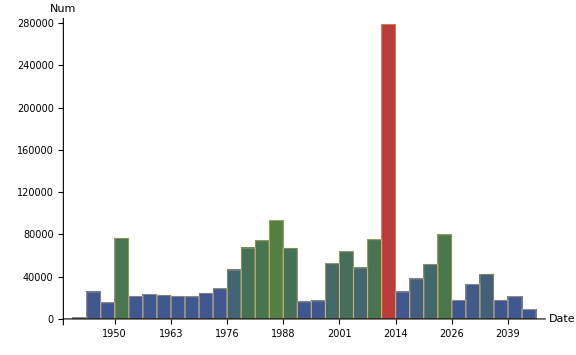

```mathematica
DateHistogram[dd,
ColorFunction->ColorData["DarkRainbow"],
ImageSize->Large,
LabelStyle->Directive[Black,Bold,15,FontFamily->"Times"],
AxesStyle->Directive[Black,Bold, 16],
AxesLabel->{"\nDate","Num"}]
```

```mathematica
weakDigits=Reverse@Sort@Select[Counts[Flatten@StringCases[psk,Repeated[DigitCharacter,{4,Infinity}]]],#>500&];
```

```mathematica
weakDigitsKey=KeyValueMap[#1->#2&,weakDigits];
```

```mathematica
susYearStr=Cases[weakDigitsKey[[;;,1]],x_/;(ToExpression[x]>1800&&ToExpression[x]<2024):>x];
```

```mathematica
susDateRemainningsMDY=
Flatten@
StringCases[
Select[
Flatten[
StringCases[
psk,
Repeated[DigitCharacter,{8}]
]
],
StringContainsQ[#,susYearStr]&
],
{__~~susYearStr~~EndOfString}
];
susDateRemainningsYMD=
Flatten@
StringCases[
Select[
Flatten[
StringCases[
psk,
Repeated[DigitCharacter,{8}]
]
],
StringContainsQ[#,susYearStr]&
],
{StartOfString~~susYearStr~~__}
];
```

```mathematica
susDateMDY=Flatten@StringCases[
Flatten@Map[dateStringSeparate8[#]&,susDateRemainningsMDY],
DatePattern[{"Month","Day","Year"}]
];
```

```mathematica
susDateYMD=Flatten@StringCases[
Flatten@Map[dateStringSeparate8[#]&,susDateRemainningsYMD],
DatePattern[{"Month","Day","Year"}]
];
```

```mathematica
susDateFin=Join[FromDateString[susDateMDY,{"Month","Day","Year"}],FromDateString[susDateYMD,{"Year","Month","Day"}]];
```

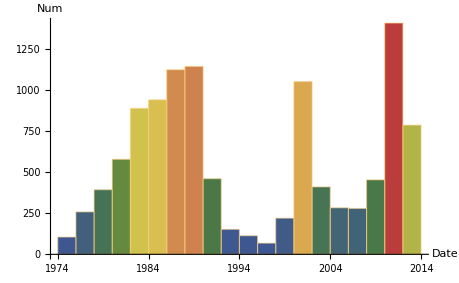

```mathematica
DateHistogram[susDateFin,
ColorFunction->ColorData["DarkRainbow"],
ImageSize->Large,
LabelStyle->Directive[Black,Bold,13,FontFamily->"Times"],
AxesStyle->Directive[Black,Bold, 13],
AxesLabel->{"\nDate","Num"}
]
```

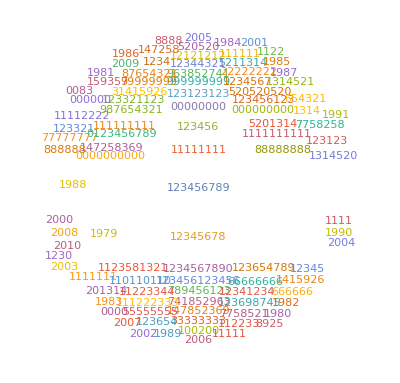

```mathematica
WordCloud[weakDigits]
```

### Word Analysis

```mathematica
engAnalysis=englishWordAnalysis[psk];
```

```mathematica
mostWords=Sort[engAnalysis,#1[[2]]>=#2[[2]]&][[;;100]];
```

```mathematica
wc=WordCloud[mostWords];
```

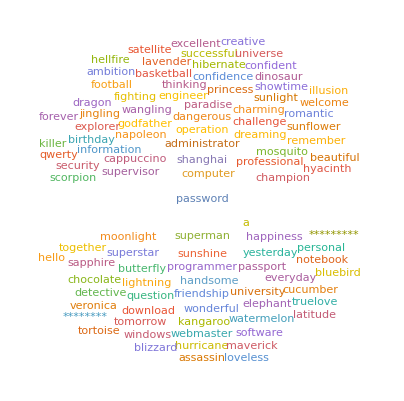
| -Graphics-

```mathematica
TableForm[{Dataset[mostWords[[;;15]]],wc},TableDirections->Row]
```

### Keyboard Analysis

```mathematica
keyAnalysis=keyboardAdjacencyAnalysis[psk];
```

```mathematica
matchedKeys=Flatten@StringCases[psk,keyboardAdjacency];
```

```mathematica
remainings=StringReplace[keyAnalysis,keyboardAdjacency->"_____"];
```

```mathematica
Sort[englishWordAnalysis[remainings],#1[[2]]>=#2[[2]]&];
```

```mathematica
Dataset[Reverse[Sort[Counts[matchedKeys]]][[;;15]]]
```

```mathematica
headAppd=StringReplace[Flatten@StringCases[remainings,StartOfString~~apd__~~Verbatim["_____"]],Verbatim["_____"]->""];
tailAppd=StringReplace[Flatten@StringCases[remainings,Verbatim["_____"]~~apd__~~EndOfString],Verbatim["_____"]->""];
```

```mathematica
TableForm[{Dataset[Reverse[Sort[Counts[Join[headAppd,tailAppd]/.""->None]]][[;;15]]],Dataset[Reverse[Sort[Counts[headAppd/.""->None]]][[;;15]]],Dataset[Reverse[Sort[Counts[tailAppd/.""->None]]][[;;15]]]},TableDirections->Row]
```

|  |

```mathematica
c0de=StringSplit[Import["(*EINZIG PATH*)darkc0de.txt"],"\n"];
```

```mathematica
(Length@psk-Length@Complement[psk,c0de])/Length[psk] 100.
```

37.303

### Association Analysis

```mathematica
usrMailName=StringReplace[usrName,"@"~~res__~~EndOfString->""];
```

```mathematica
usrMailDomain=StringReplace[usrName,StartOfString~~name__~~"@"->""];
```

```mathematica
mailDomain=(First/@StringSplit[usrMailDomain,"."]);
```

First::nofirst: {} 长度为零，没有第一个元素.

General::stop: 在本次计算中，First::nofirst 的进一步输出将被抑制.

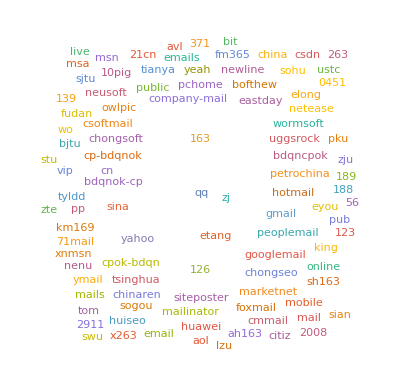

```mathematica
WordCloud[mailDomain]
```

```mathematica
LCSlistMail=Table[LongestCommonSubsequence[psk[[i]],usrMailName[[i]]],{i,Length@psk}];
LCSlistIDName=Table[LongestCommonSubsequence[psk[[i]],id[[i]]],{i,Length@psk}];
LCSlistIDNameToMail=Table[LongestCommonSubsequence[id[[i]],usrMailName[[i]]],{i,Length@psk}];
```

```mathematica
LCSposMail=Flatten@Position[LCSlistMail,x_String/;StringLength[x]>4];
LCSposIDName=Flatten@Position[LCSlistIDName,x_String/;StringLength[x]>4];
LCSposIDNameToMail=Flatten@Position[LCSlistIDNameToMail,x_String/;StringLength[x]>4];
```

```mathematica
LCSpskMail=Cases[LCSlistMail,x__/;StringLength[x]>4];
LCSpskIDName=Cases[LCSlistIDName,x__/;StringLength[x]>4];
LCSpskIDNameToMail=Cases[LCSlistIDNameToMail,x__/;StringLength[x]>4];
```

```mathematica
Length[LCSpskMail]/Length[psk] 100.
Length[LCSpskIDName]/Length[psk] 100.
Length[LCSpskIDNameToMail]/Length[psk] 100.
```

9.09083

15.4808

37.9166

```mathematica
usrName[[LCSposIDNameToMail]]//Length
```

2437520

```mathematica
tmp=id[[LCSposIDNameToMail]];
```

```mathematica
LCSIDNameToMailremains=Table[StringReplace[tmp[[i]],LCSpskIDNameToMail[[i]]->""],{i,Length@LCSpskIDNameToMail}];
tmp=id[[LCSposIDName]];
LCSIDName=Table[StringReplace[tmp[[i]],LCSpskIDName[[i]]->""],{i,Length@LCSpskIDName}];
```

```mathematica
TableForm[
{
Dataset[Reverse[Sort[Counts[LCSIDNameToMailremains/.""->"None"]]][[;;15]]],
Dataset[Reverse[Sort[Counts[LCSIDName/.""->"None"]]][[;;15]]]}
,TableDirections->Row
]
```

|

### Pinyin

```mathematica
pyJugTab=ParallelMap[(StringLength[StringJoin[StringCases[#,pyTab]]]>=4&&StringContainsQ[#,pyTab])&,psk];
```

```mathematica
pyPsk=Pick[psk,pyJugTab];
pyName=Pick[id,pyJugTab];
```

```mathematica
pyRemainings=StringReplace[pyPsk,Reverse[pyTab]->"_____"];
```

```mathematica
notPyFilteredPos=Flatten@Position[StringCases[pyRemainings,StartOfString~~Except[LetterCharacter]...~~Longest["_____"..]~~LetterCharacter...~~"_____"...~~Except[LetterCharacter]...~~EndOfString],{}];
```

```mathematica
filteredPyPosLength=Complement[Range[Length[pyPsk]],notPyFilteredPos];
```

```mathematica
pyFre=Tally[Flatten[StringCases[pyPsk[[filteredPyPosLength]],pyTab]]];
```

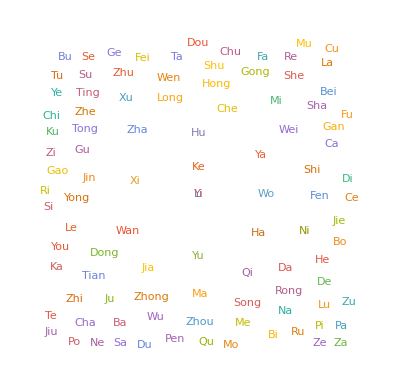

```mathematica
WordCloud[{StringReplace[pyFre[[;;,1]],StartOfString~~x:LetterCharacter:>ToUpperCase[x]],pyFre[[;;,2]]}ᵀ]
```